```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];
```

/homes/ht/Desktop/collagen/collagen_results/kappa0p12

```mathematica
DataPlots=Table[{StringSplit[FileNames["Analysis*"][[i]],"_"][[2]],
path=FileNames["Analysis*"][[i]]<>"/";
{Import[path<>"new2_force.data","Table"]}},{i,1,Length[FileNames["Analysis*"]]}];
```

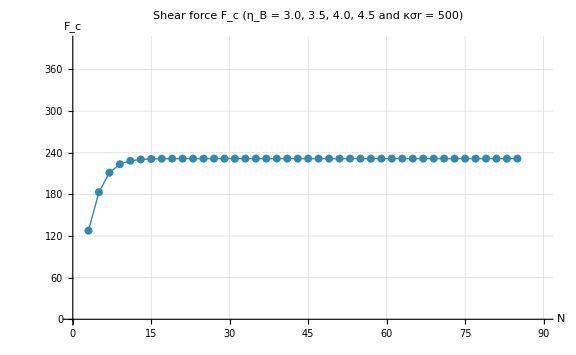

InterpolatingFunction[{{3.,85.}},<>]

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

ListLinePlot[
{
DataPlots[[1,2]][[1]]
},
PlotRange->{{0,90},{0,400}},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["F_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
Mesh->All,
PlotStyle->{RGBColor[50/255,137/255,170/255],PointSize[0.01]},
PlotLabel->Style["Shear force F_c (η_B = "<>ToString[DataPlots[[1,1]]]<>", " <>ToString[DataPlots[[2,1]]]<>", " <>ToString[DataPlots[[3,1]]]<>", " <>ToString[DataPlots[[4,1]]]<>" and κσr = "<>ToString[κσr]<>")",FontSize->fsTitle],
ImageSize->Large
]
InterF=Interpolation[DataPlots[[1,2]][[1]]]
func[x_]:=Round[If[x<80,InterF[x],InterF[85]],0.001]
```

{{0,0},{5,1},{10,12},{15,12},{20,10},{25,3},{30,14},{35,16},{40,6},{45,5},{50,13},{55,1},{60,4},{65,2},{70,0},{75,0}}

N | P(N)
0 | 0.
17 | 0.010101
33 | 0.121212
50 | 0.121212
67 | 0.10101
83 | 0.030303
100 | 0.141414
117 | 0.161616
133 | 0.0606061
150 | 0.0505051
167 | 0.131313
183 | 0.010101
200 | 0.040404
217 | 0.020202
233 | 0.
250 | 0.

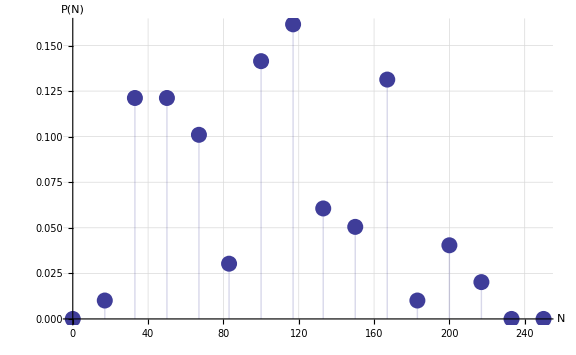

```mathematica
TropocollagenLength=300;
TotalResiduesInTC=1000;
ResiduePerNanoMeter=TotalResiduesInTC/TropocollagenLength//N;
rawData=Import["length_dist_count.dat"]

totalCount=Total[Last[Transpose[rawData]]];
rawDataWeight=Table[{Round[rawData[[idx,1]]*ResiduePerNanoMeter],(*d[[idx,2]],*)rawData[[idx,2]]/totalCount//N},{idx,1,Length[rawData]}];

Grid[Prepend[rawDataWeight,{"N","P(N)"}]]
fsTitle=24;
fsAxesLabel=18;
fs2=16;

ListPlot[rawDataWeight,PlotRange->All,AxesOrigin->{0,0},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],Filling->Axis,Mesh->All,ImageSize->Large,PlotStyle->PointSize[0.02],AxesLabel->{Style["N",FontSize->fsAxesLabel],Style["P(N)",FontSize->fsAxesLabel]},LabelStyle->{FontSize->fs2},BaseStyle->{FontFamily->"Helvetica"}]
```

{{-31.488,0.},{231.366,0.010101},{231.547,0.989899}}

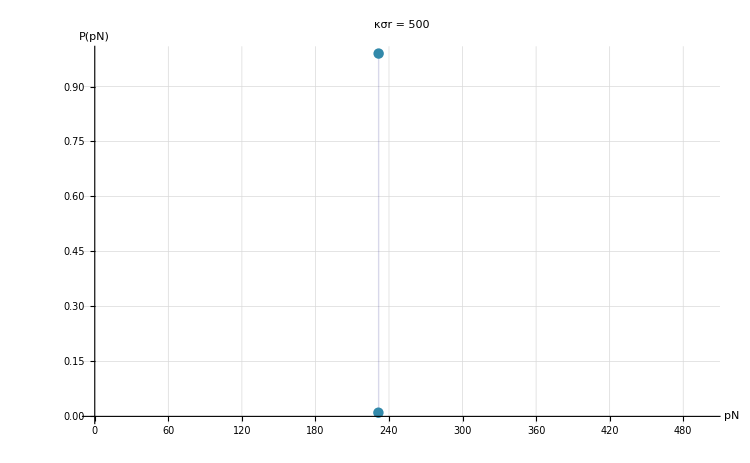

```mathematica
ForceDistributionData=Table[{func[rawDataWeight[[idx,1]]],rawDataWeight[[idx,2]]},{idx,1,Length[rawDataWeight]}];
Forces=Union[Transpose[ForceDistributionData][[1]]];
ForceProbDistributionData=Table[
{
Forces[[i]],
ListToSum=First[Transpose[Position[ForceDistributionData,Forces[[i]]]]];Sum[ForceDistributionData[[ListToSum[[idx]],2]],{idx,1,Length[ListToSum]}]
}
,{i,1,Length[Forces]}
]
ListPlot[{ForceProbDistributionData},PlotStyle->{RGBColor[50/255,137/255,170/255],PointSize[0.01]},PlotRange->{{0,500},Automatic},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],Filling->Axis,AxesLabel->{Style["pN",FontSize->fsAxesLabel],Style["P(pN)",FontSize->fsAxesLabel]},LabelStyle->{FontSize->fs2},Mesh->All,BaseStyle->{FontFamily->"Helvetica"},
PlotLabel->Style["κσr = "<>ToString[κσr],FontSize->fsTitle],ImageSize->750]
```